```mathematica
e0perf2={-.67369861*10^3,-.67467091*10^3,-.67528513*10^3,-.67557487*10^3,-.67539478*10^3,-.67436291*10^3,-.67314839*10^3,-.67068552*10^3,-.66688497*10^3}
```

{-673.699,-674.671,-675.285,-675.575,-675.395,-674.363,-673.148,-670.686,-666.885}

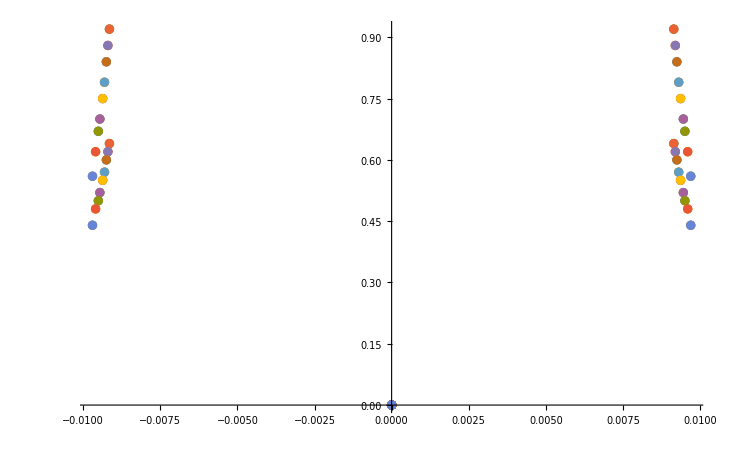

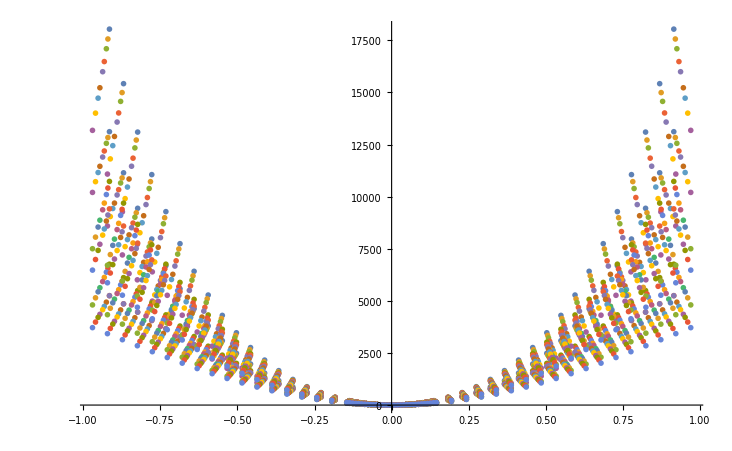

```mathematica
m={12.0107,91.224,1};
kB=1000*8.617332478*10^−5;K2meV=1000*8.617332478*10^−5;kjmol2evatom=1/(96.487*64);
e0perf={
-.67550095*10^3,-.67441442*10^3,-.67323280*10^3,-.67090290*10^3,-.66733277*10^3};
volperf={766.060,778.688,791.453,808.70835,822.656,846.590,862.257,885.289,912.673};
(*Data in*)
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/allvols"];
filesC={"C_4575","C_4600","C_4625","C_46583","C_4685_760","C_4730_1900","C_4759_2500","C_4801_3200","C_4850_3805","C_4575_110","C_4600_110","C_4625_110","C_46583_110","C_4685_760_110","C_4730_1900_110","C_4759_2500_110","C_4801_3200_110","C_4850_3805_110","C_4575_111","C_4600_111","C_4625_111","C_46583_111","C_4685_760_111","C_4730_1900_111","C_4759_2500_111","C_4801_3200_111","C_4850_3805_111"};
filesZr={"Zr_4575","Zr_4600","Zr_4625","Zr_46583","Zr_4685_760","Zr_4730_1900","Zr_4759_2500","Zr_4801_3200","Zr_4850_3805","Zr_4575_110","Zr_4600_110","Zr_4625_110","Zr_46583_110","Zr_4685_760_110","Zr_4730_1900_110","Zr_4759_2500_110","Zr_4801_3200_110","Zr_4850_3805_110","Zr_4575_111","Zr_4600_111","Zr_4625_111","Zr_46583_111","Zr_4685_760_111","Zr_4730_1900_111","Zr_4759_2500_111","zr_4801_3200_111","Zr_4850_3805_111"};
filesCh={"1.harm.C_4575","1.harm.C_4600","1.harm.C_4625","1.harm.C_46583","1.harm.C_4685_760","1.harm.C_4730_1900","1.harm.C_4759_2500","1.harm.C_4801_3200","1.harm.C_4850_3805","1.harm.C_4575_110","1.harm.C_4600_110","1.harm.C_4625_110","1.harm.C_46583_110","1.harm.C_4685_760_110","1.harm.C_4730_1900_110","1.harm.C_4759_2500_110","1.harm.C_4801_3200_110","1.harm.C_4850_3805_110","1.harm.C_4575_111","1.harm.C_4600_111","1.harm.C_4625_111","1.harm.C_46583_111","1.harm.C_4685_760_111","1.harm.C_4730_1900_111","1.harm.C_4759_2500_111","1.harm.C_4801_3200_111","1.harm.C_4850_3805_111"};
filesZrh={"1.harm.Zr_4575","1.harm.Zr_4600","1.harm.Zr_4625","1.harm.Zr_46583","1.harm.Zr_4685_760","1.harm.Zr_4730_1900","1.harm.Zr_4759_2500","1.harm.Zr_4801_3200","1.harm.Zr_4850_3805","1.harm.Zr_4575_110","1.harm.Zr_4600_110","1.harm.Zr_4625_110","1.harm.Zr_46583_110","1.harm.Zr_4685_760_110","1.harm.Zr_4730_1900_110","1.harm.Zr_4759_2500_110","1.harm.Zr_4801_3200_110","1.harm.Zr_4850_3805_110","1.harm.Zr_4575_111","1.harm.Zr_4600_111","1.harm.Zr_4625_111","1.harm.Zr_46583_111","1.harm.Zr_4685_760_111","1.harm.Zr_4730_1900_111","1.harm.Zr_4759_2500_111","1.harm.Zr_4801_3200_111","1.harm.Zr_4850_3805_111"};
Cdata=Table[ReadList[filesC[[i]],{Number, Number}],{i,1,27}];
Zrdata=Table[ReadList[filesZr[[i]],{Number, Number}],{i,1,27}];
hCdata=Table[ReadList[filesCh[[i]],{Number, Number}],{i,1,27}];
hZrdata=Table[ReadList[filesZrh[[i]],{Number, Number}],{i,1,27}];
Show[ListPlot@hCdata,ListPlot@hZrdata,PlotRange->All]
Show[ListPlot@Cdata,ListPlot@Zrdata,PlotRange->All]
```

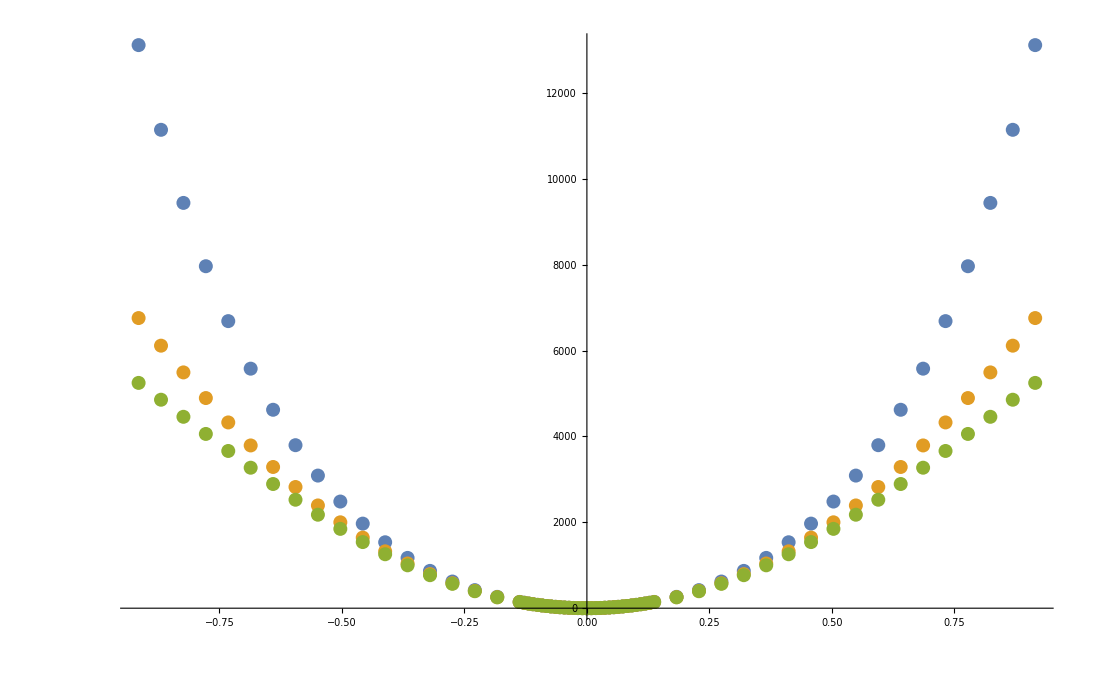

```mathematica
ListPlot[{Cdata[[1]],Cdata[[10]],Cdata[[19]],hCdata}]
```

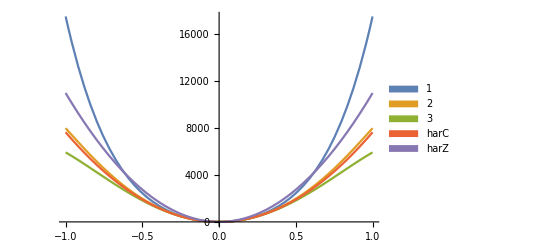

```mathematica
Plot[Evaluate@{V[1,6,x],V[1,2,x][[1]],V[2,2,x][[1]]},{x,-1,1},PlotLegends->SwatchLegend[{1,2,3,harC,harZ}]]
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Table[Fit[Cdata[[i]][[31;;36]],{x^2},x],{i,1,27}]
V[1,4,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4},x],{i,1,27,9}]
V[1,6,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6},x],{i,1,27}]
V[1,8,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,27,9}]
V[1,10,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,27,9}]
V[1,12,x_]:=Table[Fit[Cdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,27}]

V[2,2,x_]:=Table[Fit[Zrdata[[i]][[31;;36]],{x^2},x],{i,1,27}]
V[2,4,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4},x],{i,1,27,9}]
V[2,6,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6},x],{i,1,27}]
V[2,8,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8},x],{i,1,27,9}]
V[2,10,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10},x],{i,1,27,9}]
V[2,12,x_]:=Table[Fit[Zrdata[[i]],{x^2,x^4,x^6,x^8,x^10,x^12},x],{i,1,27}]
GraphicsGrid[{{Show[Plot[Evaluate@{V[1,2,x][[1]],V[1,12,x][[1]],V[1,12,x][[10]],V[1,12,x][[11]]},{x,-1.2,1.2},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Carbon potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500],Show[Plot[Evaluate@{V[2,2,x][[1]],V[2,12,x][[1]],V[2,12,x][[10]],V[2,12,x][[11]]},{x,-1.2,1.2},PlotLegends->SwatchLegend[{"harmonic","100 anharmonic","110 anharmonic","111 anharmonic"}],PlotLabel->"Zirconium potentials at 4.685Angstrom",AxesLabel->{"Angstrom","meV/atom"}],ImageSize->500]}},ImageSize->1300]
```

-Graphics-

```mathematica
V[1,2,x][[5]]
```

6264.46 x^2

```mathematica
0.5Sqrt[2Table[V[1,2,x][[i]][[1]],{i,1,9}]/m[[1]]]
0.5Sqrt[2Table[V[2,2,x][[i]][[1]],{i,1,9}]/m[[2]]]
```

{17.8061,17.4294,17.0522,16.5375,16.1489,15.5529,15.1632,14.6162,13.8778}

{7.75081,7.5489,7.34574,7.0854,6.87473,6.55869,6.35782,6.07233,5.71153}

```mathematica
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=Table[V[1,2,x][[i]][[1]],{i,1,1}]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=Table[V[2,2,x][[i]][[1]],{i,1,1}]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{7644.3}

cOmega0 in meV/Ang**2/AMU is approximately

{35.6779}

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

{10988.7}

Z_Omega_0 in meV/Ang**2/AMU is approximately

{15.5215}

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first x eigenvalues and eigenvectors*)
Neigenvalues=280;
(*Define bounds for plotting and solving eigenproblem*)
B=1.1;H=2000;
power={2,6,12};
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒallc=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x]/.i->power[[j]],{j,1,3,1}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x]/.i->power[[j]],{j,1,3,1}];
solverOptions={Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}};
```

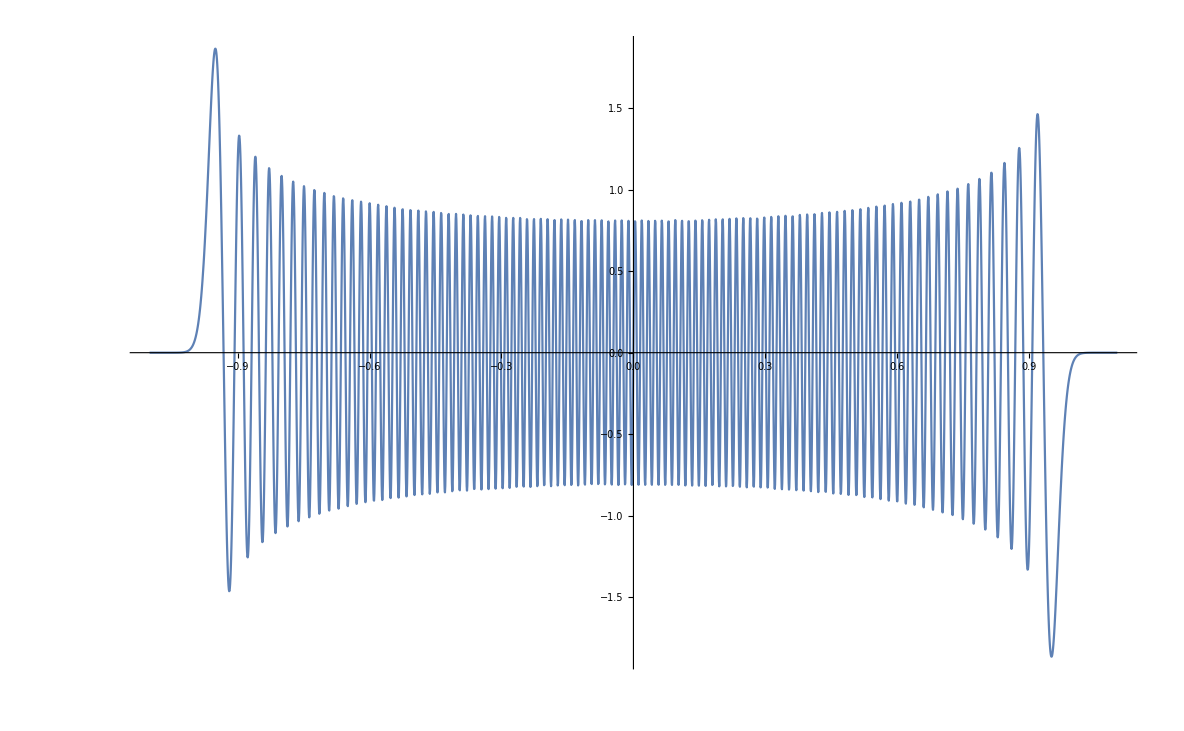

```mathematica
test=Table[NDEigensystem[ℒallc[[1]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,1}];
Plot[test[[1]][[2]][[200]],{x,-B,B},PlotRange->All]
```

```mathematica
(*ℒallc[[1=harmonic]]ℒallc[[2=anharmonic 6th order,3=anharmonic 12th order]]*)
char1d=Table[NDEigensystem[ℒallc[[1]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,27}];
c6anh1d=Table[NDEigensystem[ℒallc[[2]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,27}];
c12anh1d=Table[NDEigensystem[ℒallc[[3]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,27}];
DumpSave["dump.char1d.mx",char1d]
DumpSave["dump.c6anh1d.mx",canh1d]
DumpSave["dump.c12anh1d.mx",canh1d]
```

{{1}}
 |  |  |  |

{canh1d}

{canh1d}

```mathematica
zhar1d=Table[NDEigensystem[ℒallz[[1]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,27}];
z6anh1d=Table[NDEigensystem[ℒallz[[2]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,27}];
z12anh1d=Table[NDEigensystem[ℒallz[[3]][[i]],u[x],{x,-B,B},Neigenvalues,Evaluate@solverOptions],{i,1,27}];
DumpSave["dump.zhar1d.mx",char1d]
DumpSave["dump.z6anh1d.mx",canh1d]
DumpSave["dump.z12anh1d.mx",canh1d]
```

{{{{17.839,53.5169,89.1948,124.873,160.551,196.229,231.907,267.585,303.262,338.94,374.618,410.296,445.974,481.652,517.33,250,9471.53,9510.88,9550.65,9590.82,9631.34,9672.21,9713.41,9754.93,9796.74,9838.86,9881.25,9923.93,9966.87,10010.1,10053.5},{1}},26}}
 |  |  |  |

{canh1d}

{canh1d}

```mathematica
Get["dump.char1d.mx"]
Get["dump.c6anh1d.mx"]
Get["dump.c12anh1d.mx"]
Get["dump.zhar1d.mx"]
Get["dump.z6anh1d.mx"]
Get["dump.z12anh1d.mx"]
```

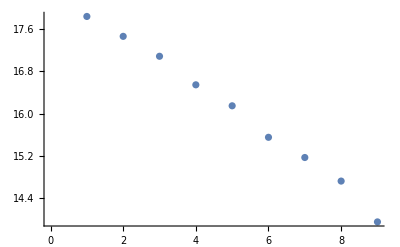

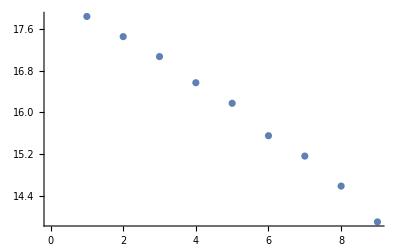

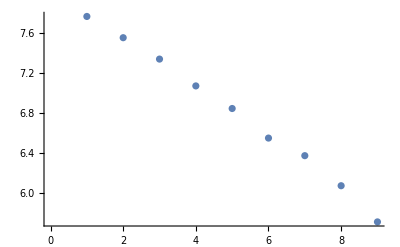

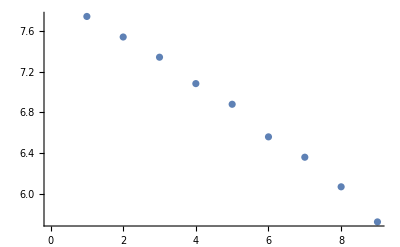

```mathematica
ListPlot@Table[char1d[[i]][[1]][[1]],{i,1,9}]
ListPlot@Table[c12anh1d[[i]][[1]][[1]],{i,1,9}]
ListPlot@Table[zhar1d[[i]][[1]][[1]],{i,1,9}]
ListPlot@Table[z12anh1d[[i]][[1]][[1]],{i,1,9}]
```

```mathematica
(*NOTE also rescale the anharmonic frequencies to tend exactly to the harmonic freqs in the limit of low T ie the first mode*)
(*... there is a small random error 0.05% at for omega0, but over 200 eigenvalues gets amplied so messes up volume order of distributions*)
(*Exmaple:*)
c12anh1d[[1]][[1]][[1;;20]]
c12anh1d[[1]][[1]][[1;;20]]/c12anh1d[[1]][[1]][[1]]
char1d[[1]][[1]][[1]]*c12anh1d[[1]][[1]][[1;;20]]/c12anh1d[[1]][[1]][[1]]
```

{17.8304,53.5584,89.4203,125.415,161.542,197.799,234.187,270.703,307.347,344.118,381.015,418.037,455.184,492.454,529.847,567.361,604.996,642.752,680.627,718.62}

{1.,3.00377,5.01505,7.03379,9.05991,11.0934,13.1341,15.1821,17.2373,19.2995,21.3689,23.4452,25.5286,27.6188,29.716,31.8199,33.9306,36.0481,38.1723,40.3031}

{17.839,53.5842,89.4634,125.475,161.62,197.894,234.299,270.833,307.495,344.284,381.199,418.239,455.403,492.691,530.102,567.634,605.288,643.061,680.954,718.966}

```mathematica
maxval=250;
(*Fix harmonic to use perfect summation from omega0*)
char1de=Table[Table[char1d[[i]][[1]][[1]]*2(j-0.5),{j,1,maxval}],{i,1,27}];
c6anh1de=Table[char1d[[i]][[1]][[1]]*c6anh1d[[i]][[1]][[1;;maxval]]/c6anh1d[[i]][[1]][[1]],{i,1,27}];
c12anh1de=Table[char1d[[i]][[1]][[1]]*c12anh1d[[i]][[1]][[1;;maxval]]/c12anh1d[[i]][[1]][[1]],{i,1,27}];
zhar1de=Table[Table[zhar1d[[i]][[1]][[1]]*2(j-0.5),{j,1,maxval}],{i,1,27}];
z6anh1de=Table[zhar1d[[i]][[1]][[1]]*z6anh1d[[i]][[1]][[1;;maxval]]/z6anh1d[[i]][[1]][[1]],{i,1,27}];
z12anh1de=Table[zhar1d[[i]][[1]][[1]]*z12anh1d[[i]][[1]][[1;;maxval]]/z12anh1d[[i]][[1]][[1]],{i,1,27}];
```

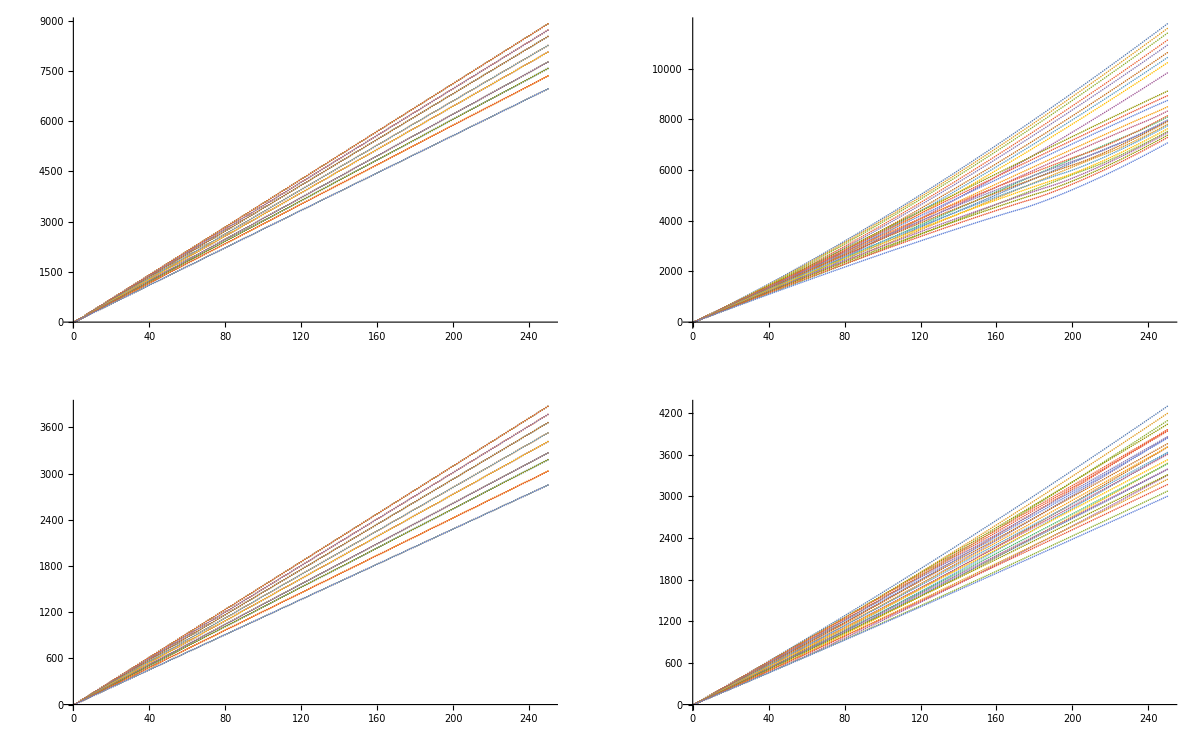

```mathematica
GraphicsGrid[{{ListPlot[char1de],ListPlot[c12anh1de[[1;;27]]]},{ListPlot[zhar1de],ListPlot[z12anh1de[[1;;27]]]}},ImageSize->1200]
```

```mathematica
GraphicsGrid[{Table[Show[ListPlot[char1de[[i]],PlotStyle->{Red},PlotLegends->SwatchLegend[{"Harmonic"}],ImageSize->400],ListPlot[{c12anh1de[[i]],c12anh1de[[9+i]],c12anh1de[[18+i]]},PlotLegends->SwatchLegend[{"Zr 001 anharmonic","Zr 011 anharmonic","Zr 111 anharmonic"}]]],{i,1,9}]},ImageSize->5000]
GraphicsGrid[{Table[ListPlot[{c12anh1de[[i]]/char1de[[i]],c12anh1de[[9+i]]/char1de[[i]],c12anh1de[[18+i]]/char1de[[i]]},ImageSize->400,PlotLegends->SwatchLegend[{"Zr 001 anharmonic","Zr 011 anharmonic","Zr 111 anharmonic"}]],{i,1,9}]},ImageSize->5000]
```

-Graphics-

-Graphics-

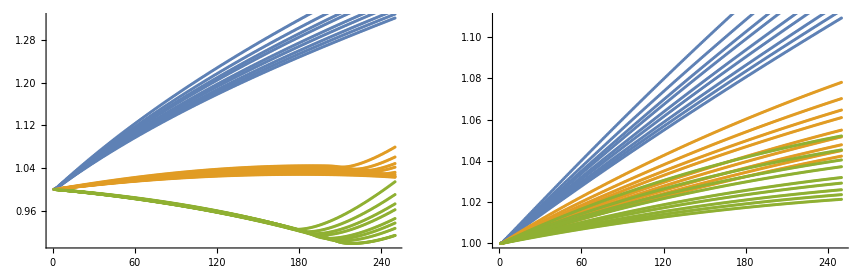

```mathematica
GraphicsGrid[{{Show@Table[ListPlot[{c12anh1de[[i]]/char1de[[i]],c12anh1de[[9+i]]/char1de[[i]],c12anh1de[[18+i]]/char1de[[i]]},ImageSize->400],{i,1,9}],Show@Table[ListPlot[{z12anh1de[[i]]/zhar1de[[i]],z12anh1de[[9+i]]/zhar1de[[i]],z12anh1de[[18+i]]/zhar1de[[i]]},ImageSize->400],{i,1,9}]}}]
```

```mathematica
fr[T_,spectrumZ_,spectrumC_,maxEigen_,xFactor_,pFactor_]:=-K2meV*(pFactor)*T*Log[{Total[Exp[-xFactor*spectrumZ/(K2meV*T)]],Total[Exp[-xFactor*spectrumC/(K2meV*T)]]}]
```

```mathematica
Table[{t,Total@fr[t,z12anh1de[[1]],c12anh1de[[1]],150,2,1.5]},{t,4000,4000}]
Table[{t,Total@fr[t,z12anh1de[[1]],c12anh1de[[1]],275,2,1.5]},{t,4000,4000}]
```

{{4000,-2044.84}}

{{4000,-2044.84}}

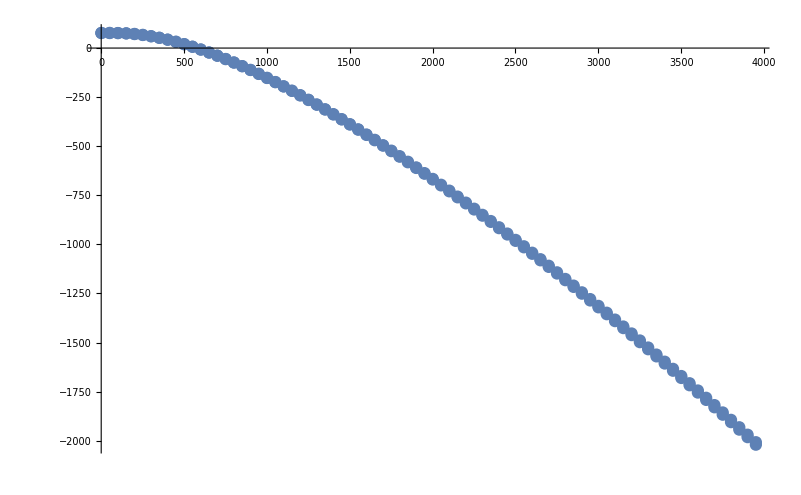

```mathematica
Show[ListPlot[Table[{t,Total@fr[t,zhar1de[[1]],char1de[[1]],150,2,1.5]},{t,1,4000,50}]],ListPlot[Table[{t,Total@fr[t,z12anh1de[[1]],c12anh1de[[1]],150,2,1.5]},{t,1,4000,50}]]]
```

{4.575Å ⟨001⟩,4.600Å ⟨001⟩,4.625Å ⟨001⟩,4.658Å ⟨001⟩,4.685Å ⟨001⟩,4.730Å ⟨001⟩,4.759Å ⟨001⟩,4.801Å ⟨001⟩,4.850Å ⟨001⟩,4.575Å ⟨011⟩,4.600Å ⟨011⟩,4.625Å ⟨011⟩,4.658Å ⟨011⟩,4.685Å ⟨011⟩,4.730Å ⟨011⟩,4.759Å ⟨011⟩,4.801Å ⟨011⟩,4.850Å ⟨011⟩,4.575Å ⟨111⟩,4.600Å ⟨111⟩,4.625Å ⟨111⟩,4.658Å ⟨111⟩,4.685Å ⟨111⟩,4.730Å ⟨111⟩,4.759Å ⟨111⟩,4.801Å ⟨111⟩,4.850Å ⟨111⟩}

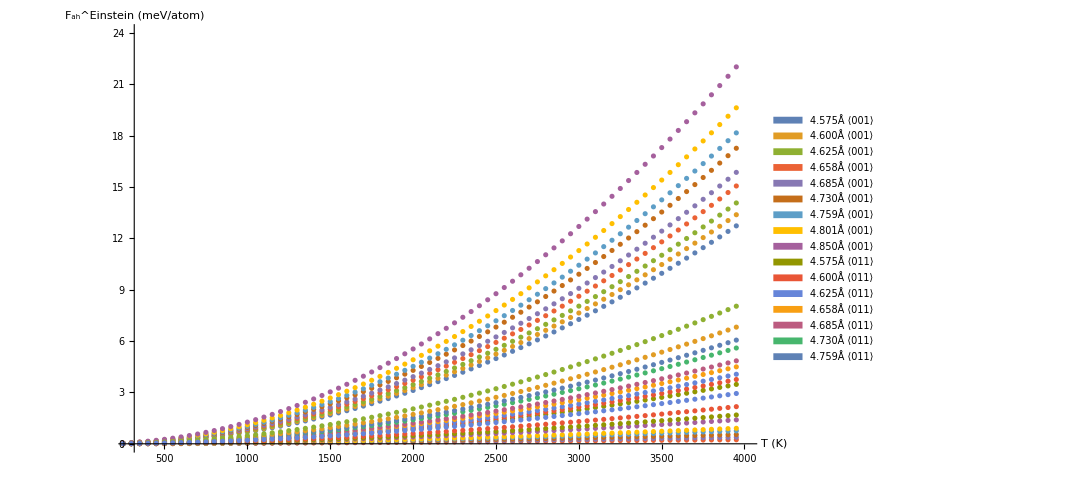

```mathematica
vols={"4.575Å","4.600Å","4.625Å","4.658Å","4.685Å","4.730Å","4.759Å","4.801Å","4.850Å"};
dirs={" ⟨001⟩"," ⟨011⟩"," ⟨111⟩"};maxT=4000;minT=300;dT=100;
plab=Flatten@Table[StringJoin[vols[[i]],dirs[[j]]],{j,1,3},{i,1,9}]
ListPlot[Table[Table[{t,Total@fr[t,z12anh1de[[i]],c12anh1de[[i]],150,2,1.5]-Total@fr[t,zhar1de[[i]],char1de[[i]],150,2,1.5]},{t,1,4000,50}],{i,1,27}],PlotRange->{{minT,maxT},{0,24}},PlotLegends->SwatchLegend[plab],ImageSize->800,AxesLabel->{"T (K)","F_ah^Einstein (meV/atom)"},PlotStyle->"Thick"]
```

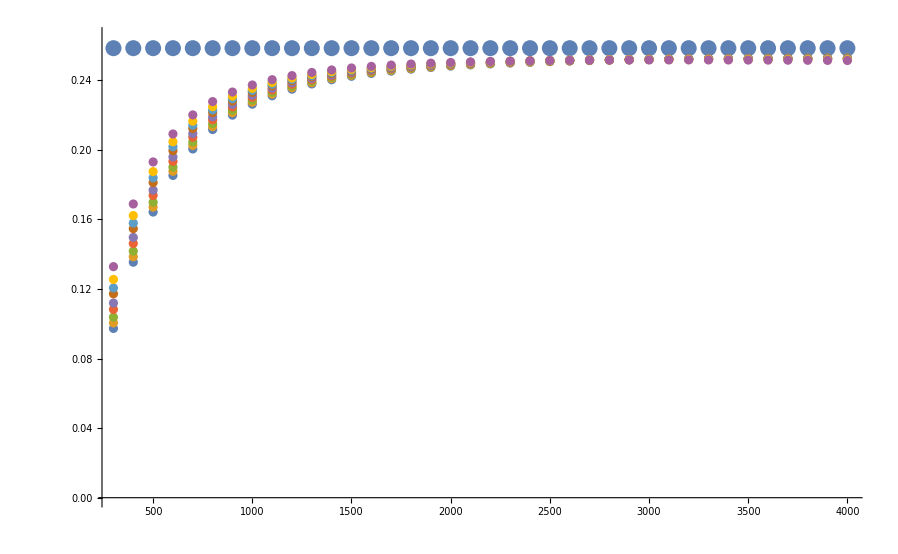

```mathematica
Show[ListPlot[Table[{T,3kB},{T,minT,maxT,dT}],PlotRange->{All,{0,0.265}}],ListPlot[Table[ Table[{T,t*D[-D[Total@fr[t,z12anh1de[[vol]],c12anh1de[[vol]],150,4,1.5],t],t]}/.t->T,{T,minT,maxT,dT}],{vol,1,9}]]]
```

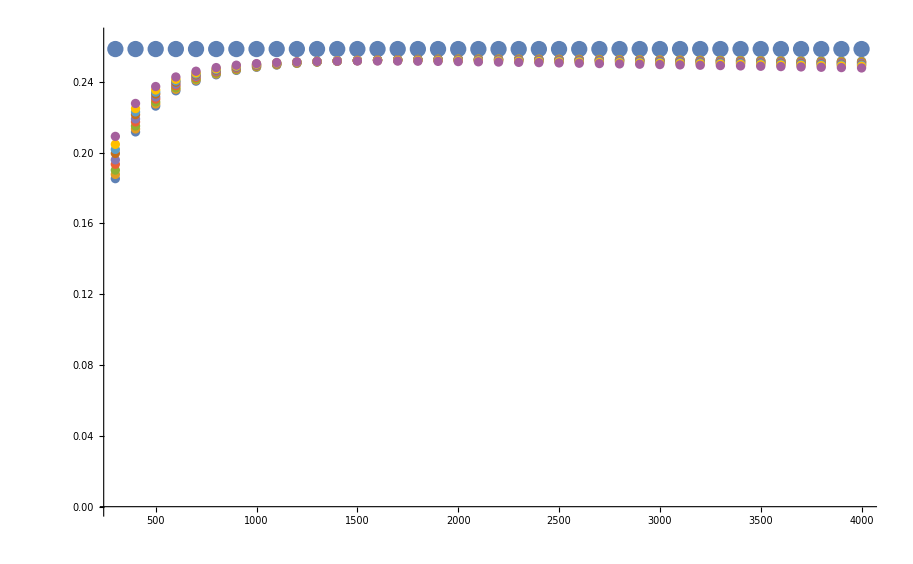

```mathematica
Show[ListPlot[Table[{T,3kB},{T,minT,maxT,dT}],PlotRange->{All,{0,0.265}}],ListPlot[Table[ Table[{T,t*D[-D[Total@fr[t,z12anh1de[[vol]],c12anh1de[[vol]],150,2,1.5],t],t]}/.t->T,{T,minT,maxT,dT}],{vol,1,9}]]]
```

```mathematica
e0perf
```

{-673.821,-674.791,-675.402,-675.686,-675.501,-674.414,-673.233,-670.903,-667.333}

```mathematica
volperf
```

{766.06,778.688,791.453,808.708,822.656,846.59,862.257,885.289,912.673}

822.578-4.8031 x+0.00499217 x^2-1.66738×10^-6 x^3

20665.2-12550.3 x+2437.56 x^2-156.059 x^3

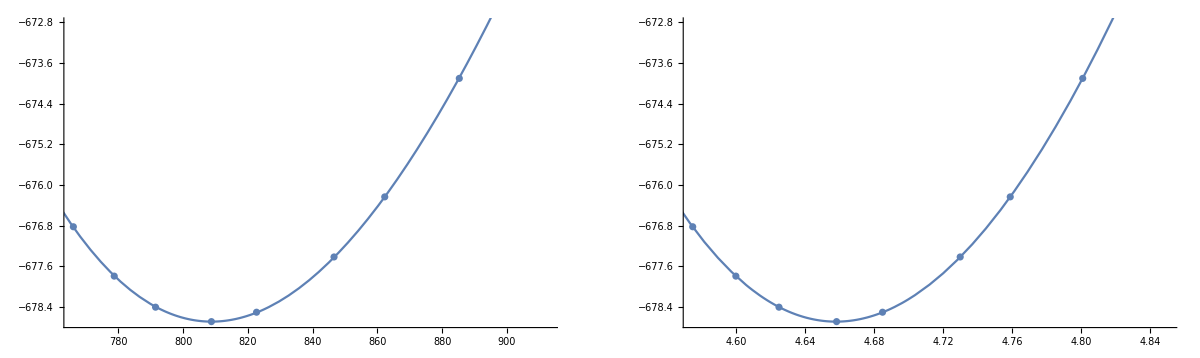

```mathematica
e0volfit=Fit[Transpose[{volperf,e0perf}],{1,x,x*x,x*x*x},x];
e0afit=Fit[Transpose[{0.5(volperf^(1/3)),e0perf}],{1,x,x*x,x*x*x},x];
e0volfit
e0afit
GraphicsGrid[{{Show[ListPlot[Transpose[{volperf,e0perf}]],Plot[e0volfit,{x,750,900}]],Show[ListPlot[Transpose[{0.5(volperf^(1/3)),e0perf}]],Plot[e0afit,{x,4.5,4.9}]]}},ImageSize->1200]
```

```mathematica
e0afit
eafitMin=FindMinimum[Evaluate@e0afit,x][[1]]
e0=e0perf[[1;;9]]-eafitMin
a0=0.5(volperf^(1/3))
```

20665.2-12550.3 x+2437.56 x^2-156.059 x^3

-678.686

{1.8655,0.894896,0.284126,0.000286066,0.185056,1.27159,2.45321,4.78311,8.35324}

{4.575,4.6,4.625,4.65837,4.685,4.73,4.759,4.801,4.85}

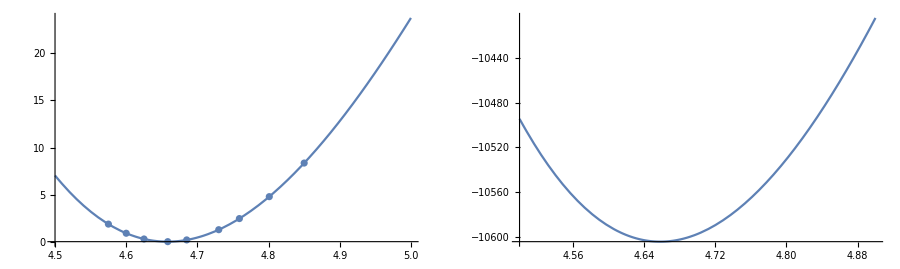

```mathematica
GraphicsGrid[{{Show[Plot[Evaluate@Fit[Transpose[{a0,e0}],{1,x,x*x,x*x*x},x],{x,4.5,5}],ListPlot[Transpose[{a0,e0}]]],Plot[e0afit*1000/64,{x,4.5,4.9}]}},ImageSize->900]
```

```mathematica
Table[Table[{t,1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],150,2,1.5]},{t,1,10,5}],{i,4,4}]
```

{{{1,70.8459},{6,70.8459}}}

```mathematica
Table[Table[{t,1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],150,1,3]},{t,1,10,5}],{i,4,4}]
```

{{{1,70.8459},{6,70.8459}}}

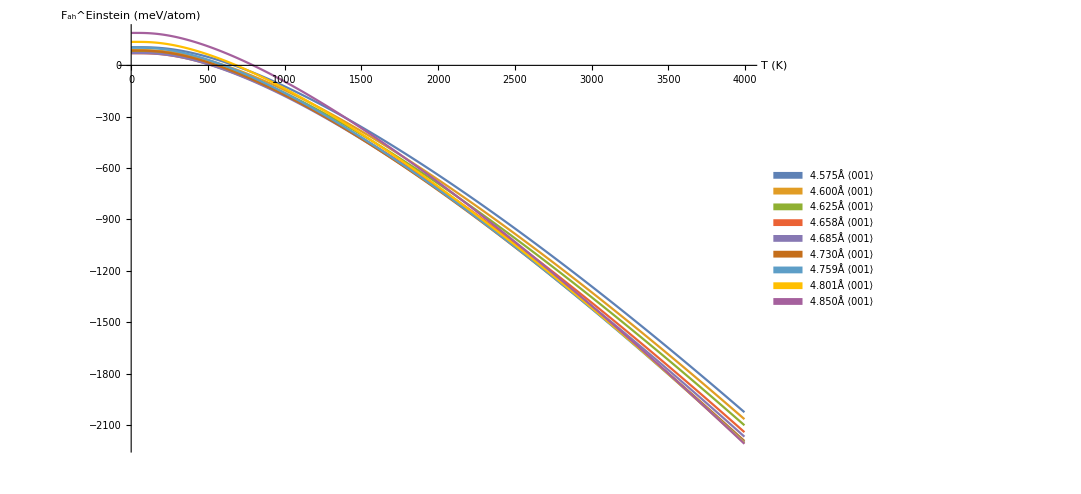

```mathematica
ListLinePlot[Table[Table[{t,1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],150,2,1.5]},{t,1,4000,5}],{i,1,9}],PlotLegends->SwatchLegend[plab],ImageSize->800,AxesLabel->{"T (K)","F_ah^Einstein (meV/atom)"},PlotStyle->PointSize[0.2]]
```

783293.-482127. x+98611.9 x^2-6722.74 x^3

{-678.686,{x→4.6581}}

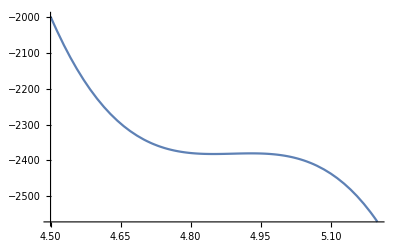

{-2382.37,{x→4.84891}}

-Graphics-

```mathematica
fit=Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],150,2,1.5]},{i,1,9}]/.t->4200,{1,x,x*x,x*x*x},x]
Minimize[e0afit,x]
Plot[fit,{x,4.5,5.2}]
Minimize[{fit,4.5<x<4.9},x]
Plot[fit,{x,4.5,5.2}]
```

```mathematica
temps[t_]:=1+9.6t^2
tlist=Table[temps[t],{t,0,22}]
fitT=Table[Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],150,2,1.5]},{i,1,9}]/.t->tlist[[j]],{1,x,x*x,x*x*x},x],{j,1,22}];
fitTanh=Table[Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,z12anh1de[[i]],c12anh1de[[i]],150,2,1.5]},{i,1,9}]/.t->tlist[[j]],{1,x,x*x,x*x*x},x],{j,1,22}];
```

{1.,10.6,39.4,87.4,154.6,241.,346.6,471.4,615.4,778.6,961.,1162.6,1383.4,1623.4,1882.6,2161.,2458.6,2775.4,3111.4,3466.6,3841.,4234.6,4647.4}

```mathematica
minaData=Table[Minimize[{fitT[[i]],4.575<x<4.9},x],{i,1,22}]
minaDataanh=Table[Minimize[{fitTanh[[i]],4.575<x<4.9},x],{i,1,22}]
minA=Table[minaData[[i]][[2]][[1]][[2]],{i,1,22}]
mine0=Table[minaData[[i]][[1]],{i,1,22}]
minAanh=Table[minaDataanh[[i]][[2]][[1]][[2]],{i,1,22}]
mine0anh=Table[minaDataanh[[i]][[1]],{i,1,22}]
```

{{70.5795,{x→4.66622}},{70.5795,{x→4.66622}},{70.5781,{x→4.66622}},{70.3001,{x→4.66635}},{67.8286,{x→4.66705}},{59.8513,{x→4.6686}},{42.9746,{x→4.67106}},{14.3943,{x→4.67437}},{-28.0631,{x→4.67845}},{-86.1256,{x→4.68325}},{-161.231,{x→4.68877}},{-254.626,{x→4.69499}},{-367.42,{x→4.70196}},{-500.632,{x→4.70973}},{-655.206,{x→4.71839}},{-832.042,{x→4.72808}},{-1032.01,{x→4.73902}},{-1255.97,{x→4.75157}},{-1504.8,{x→4.76632}},{-1779.49,{x→4.78447}},{-2081.22,{x→4.80903}},{-2412.09,{x→4.85602}}}

{{70.5795,{x→4.66622}},{70.5795,{x→4.66622}},{70.5781,{x→4.66622}},{70.3007,{x→4.66635}},{67.8342,{x→4.66705}},{59.8746,{x→4.66859}},{43.04,{x→4.67104}},{14.5398,{x→4.67432}},{-27.7821,{x→4.67837}},{-85.6332,{x→4.68312}},{-160.427,{x→4.68855}},{-253.383,{x→4.69466}},{-365.579,{x→4.70147}},{-497.997,{x→4.70902}},{-651.539,{x→4.71738}},{-827.056,{x→4.72666}},{-1025.36,{x→4.73702}},{-1247.23,{x→4.74873}},{-1493.47,{x→4.76221}},{-1764.9,{x→4.77825}},{-2062.46,{x→4.79852}},{-2387.43,{x→4.82816}}}

{4.66622,4.66622,4.66622,4.66635,4.66705,4.6686,4.67106,4.67437,4.67845,4.68325,4.68877,4.69499,4.70196,4.70973,4.71839,4.72808,4.73902,4.75157,4.76632,4.78447,4.80903,4.85602}

{70.5795,70.5795,70.5781,70.3001,67.8286,59.8513,42.9746,14.3943,-28.0631,-86.1256,-161.231,-254.626,-367.42,-500.632,-655.206,-832.042,-1032.01,-1255.97,-1504.8,-1779.49,-2081.22,-2412.09}

{4.66622,4.66622,4.66622,4.66635,4.66705,4.66859,4.67104,4.67432,4.67837,4.68312,4.68855,4.69466,4.70147,4.70902,4.71738,4.72666,4.73702,4.74873,4.76221,4.77825,4.79852,4.82816}

{70.5795,70.5795,70.5781,70.3007,67.8342,59.8746,43.04,14.5398,-27.7821,-85.6332,-160.427,-253.383,-365.579,-497.997,-651.539,-827.056,-1025.36,-1247.23,-1493.47,-1764.9,-2062.46,-2387.43}

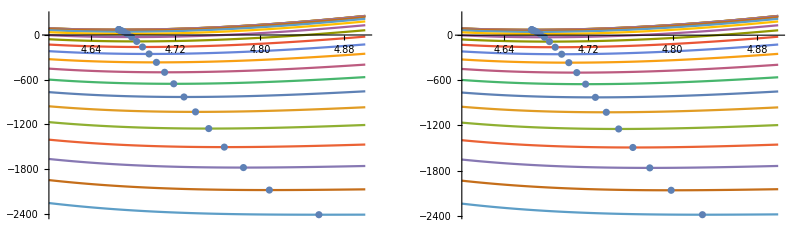

```mathematica
grunHar=ListPlot@Transpose[{minA,mine0}];
grunAnh=ListPlot@Transpose[{minAanh,mine0anh}];
GraphicsGrid[{{Show[Plot[fitT,{x,4.6,4.9}],grunHar],Show[Plot[fitTanh,{x,4.6,4.9}],grunAnh]}},ImageSize->800]
```

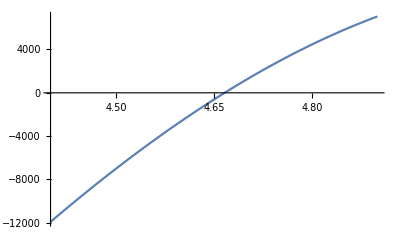

{0.,0.,-1.68398×10^-8,-2.34542×10^-7,-6.11231×10^-8,0.0043992,-0.000883322,6.12869×10^-7,0.,-0.00464717,-4.45818×10^-7,-0.00298779,-0.00389361,-0.00192194,3.21062×10^-7,0.,3.00674×10^-7,-7.19102×10^-8,0.,0.,0.,-0.0000994735}

4.66622

```mathematica
(*Maxwell identity:
G(T)=F(V,T)-V*dF/dV
http://www.tandfonline.com/doi/pdf/10.1080/01418638108222168?needAccess=true  J Harding paper
*)
Plot[Evaluate[x*D[fitT[[1]],x]],{x,4.4,4.9}]
Table[Evaluate[x*D[fitT[[i]],x]]/.x->minA[[i]],{i,1,22}]
minA[[1]]
```

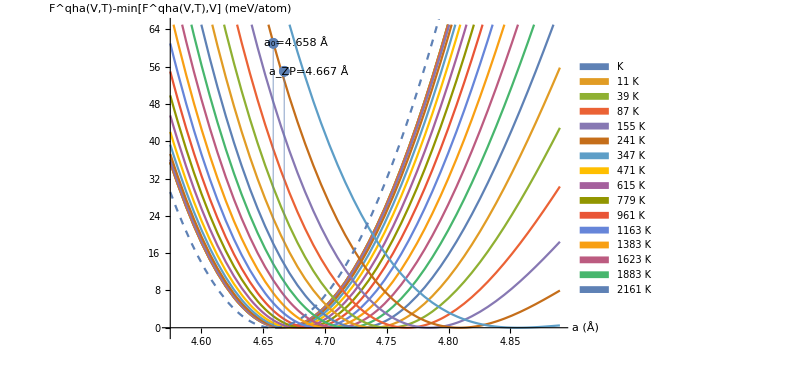

```mathematica
Show[Plot[Evaluate[fitT-mine0],{x,4.575,4.89},PlotLegends->SwatchLegend[Round[tlist]"K"],PlotRange->{Automatic,{-1,65}},AxesLabel->{"a (Å)","F^qha(V,T)-min[F^qha(V,T),V]\n (meV/atom)"},ImageSize->600],ListPlot[{{4.6583,61}},Filling->Bottom],Graphics[{Text["a_0=4.658 Å",{4.677,61}]}],ListPlot[{{4.6672,55}},Filling->Bottom],Graphics[{Text["a_ZP=4.667 Å",{4.687,55}]}],Plot[Evaluate[(e0afit-Minimize[e0afit,x][[1]])*1000/64],{x,4.575,4.85},PlotStyle->Dashed,PlotLegends->{"E_0(V)"}]]
```

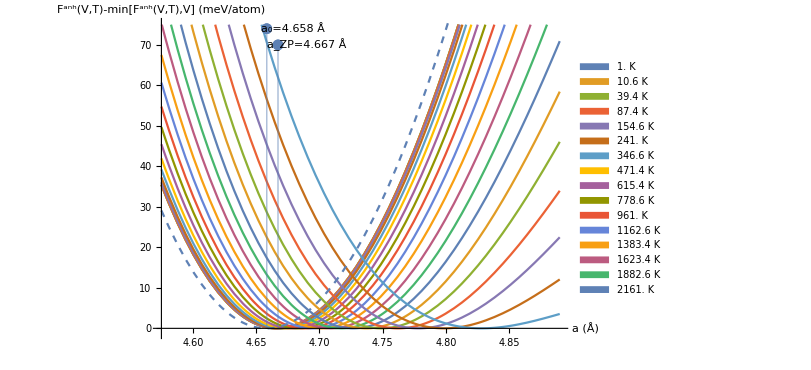

```mathematica
Show[Plot[Evaluate[fitTanh-mine0anh],{x,4.575,4.89},PlotLegends->SwatchLegend[tlist"K"],PlotRange->{Automatic,{-1,75}},AxesLabel->{"a (Å)","F^anh(V,T)-min[F^anh(V,T),V]\n (meV/atom)"},ImageSize->600],ListPlot[{{4.6583,74}},Filling->Bottom],Graphics[{Text["a_0=4.658 Å",{4.679,74}]}],ListPlot[{{4.6672,70}},Filling->Bottom],Graphics[{Text["a_ZP=4.667 Å",{4.6897,70}]}],Plot[Evaluate[(e0afit-Minimize[e0afit,x][[1]])*1000/64],{x,4.575,4.89},PlotStyle->Dashed,PlotLegends->{"E_0(V)"}]]
```

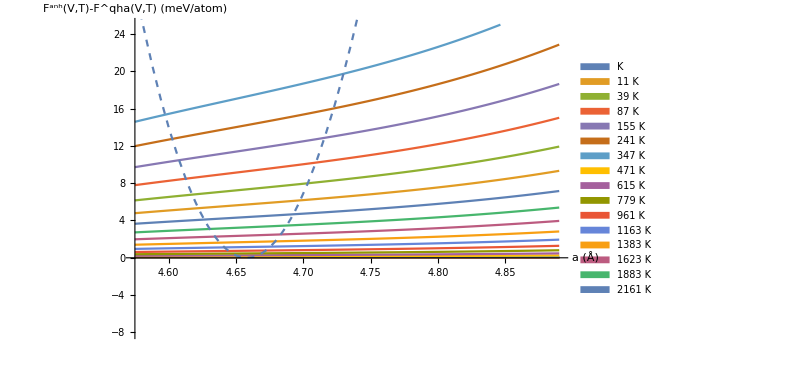

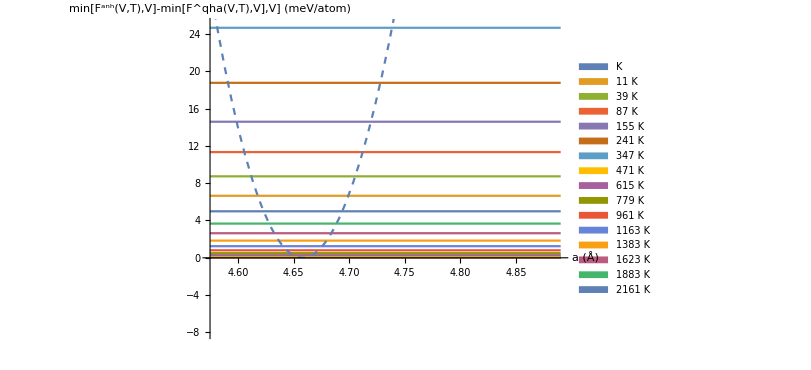

```mathematica
Show[Plot[Evaluate[(fitTanh)-(fitT)],{x,4.575,4.89},PlotLegends->SwatchLegend[Round[tlist]"K"],PlotRange->{Automatic,{-8,25}},AxesLabel->{"a (Å)","F^anh(V,T)-F^qha(V,T)\n (meV/atom)"},ImageSize->600],Plot[Evaluate[(e0afit-Minimize[e0afit,x][[1]])*1000/64],{x,4.575,4.89},PlotStyle->Dashed,PlotLegends->{"E_0(V)"}]]
Show[Plot[Evaluate[(mine0anh)-(mine0)],{x,4.575,4.89},PlotLegends->SwatchLegend[Round[tlist]"K"],PlotRange->{Automatic,{-8,25}},AxesLabel->{"a (Å)","min[F^anh(V,T),V]-min[F^qha(V,T),V],V]\n (meV/atom)"},ImageSize->600],Plot[Evaluate[(e0afit-Minimize[e0afit,x][[1]])*1000/64],{x,4.575,4.89},PlotStyle->Dashed,PlotLegends->{"E_0(V)"}]]
```

```mathematica
tmax=4010;
tlistall=Table[t,{t,1,tmax}];
fitTall=Table[Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],150,2,1.5]},{i,1,9}]/.t->T,{1,x,x*x,x*x*x},x],{T,1,tmax}];
interTall=Table[Interpolation[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,zhar1de[[i]],char1de[[i]],150,2,1.5]},{i,1,9}]/.t->T],{T,3700,tmax}];
```

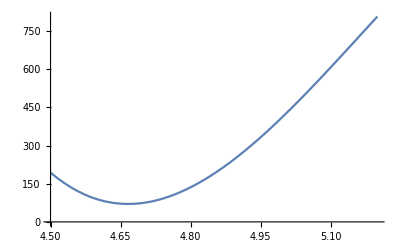

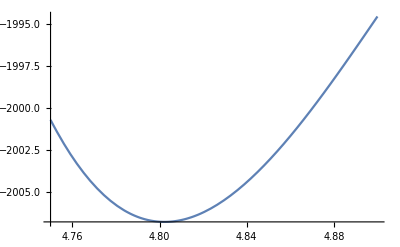

{-2006.75,{x→4.80226}}

{-2047.57,{x→4.80589}}

InterpolatingFunction::dmval: Input value {4.87359} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.87127} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.87859} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-2011.71,{x→4.89}}

InterpolatingFunction::dmval: Input value {4.87359} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.87127} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.87859} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{-2054.05,{x→4.89}}

```mathematica
Plot[fitTall[[1]],{x,4.5,5.2}]
Plot[fitTall[[3750]],{x,4.75,4.9}]
Minimize[{fitTall[[3750]],4.64<x<4.89},x]
NMinimize[{fitTall[[3800]],4.64<x<4.89},x]
Minimize[{interTall[[50]][x],4.64<x<4.89},x]
NMinimize[{interTall[[100]][x],4.64<x<4.89},x]
```

```mathematica
fitTallanh=Table[Fit[Table[{a0[[i]],1000/64*e0[[i]]+Total@fr[t,z12anh1de[[i]],c12anh1de[[i]],150,2,1.5]},{i,1,9}]/.t->T,{1,x,x*x,x*x*x},x],{T,1,tmax}];
minaDataTall=Table[Minimize[{fitTall[[i]],4.64<x<4.89},x,WorkingPrecision->20],{i,1,tmax}];
minaDataTallanh=Table[Minimize[{fitTallanh[[i]],4.64<x<4.89},x,WorkingPrecision->20],{i,1,tmax}];
minAall=Table[minaDataTall[[i]][[2]][[1]][[2]],{i,1,tmax}];
mine0all=Table[minaDataTall[[i]][[1]],{i,1,tmax}];
minAallanh=Table[minaDataTallanh[[i]][[2]][[1]][[2]],{i,1,tmax}];
mine0allanh=Table[minaDataTallanh[[i]][[1]],{i,1,tmax}];
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

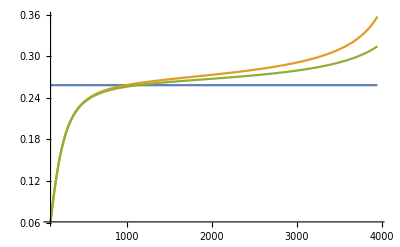

```mathematica
Plot[{kB*3,Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0all}]][x],x],x]],Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0allanh}]][x],x],x]]},{x,100,3950},PlotRange->All]
```

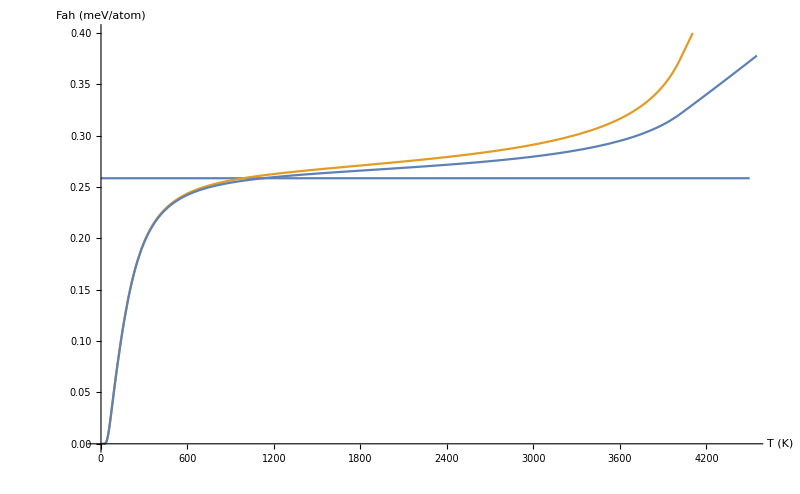

```mathematica
minty=1;maxty1=4500;maxty2=4550;
Show[Plot[{kB*3,Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0all}]][x],x],x]]},{x,minty,maxty1},PlotRange->{{minty,maxty1},{0.00,0.4}},AxesLabel->{"T (K)","Fah (meV/atom)"}],
Plot[{Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0allanh}]][x],x],x]]},{x,minty,maxty2},PlotRange->{{minty,maxty2},{0.00,0.4}}],ImageSize->800]
```

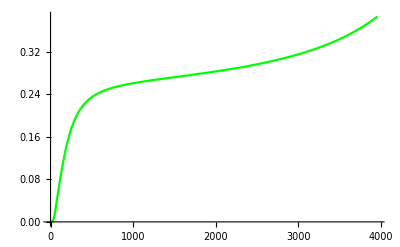

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/output_qha_700eV_666kp/QHA_PERF"];
qhaCp=ReadList["Cp-temperature.dat",{Number, Number}];
cpQHAnnormal=ListLinePlot[Transpose[{Transpose[qhaCp][[1]],kjmol2evatom*Transpose[qhaCp][[2]]}],PlotStyle->Green]
```

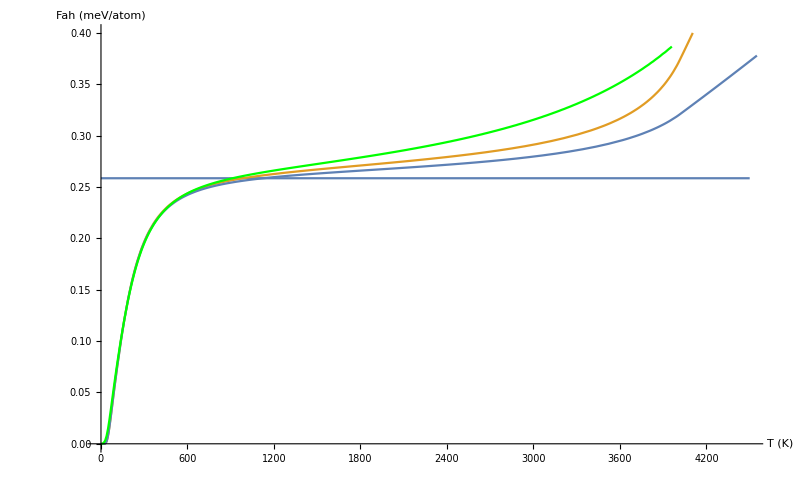

```mathematica
Show[Plot[{kB*3,Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0all}]][x],x],x]]},{x,minty,maxty1},PlotRange->{{minty,maxty1},{0.00,0.4}},AxesLabel->{"T (K)","Fah (meV/atom)"}],
Plot[{Evaluate[-x*D[D[Interpolation[Transpose[{tlistall,mine0allanh}]][x],x],x]]},{x,minty,maxty2},PlotRange->{{minty,maxty2},{0.00,0.4}}],cpQHAnnormal,ImageSize->800]
```